## 2025 - 08 - 19

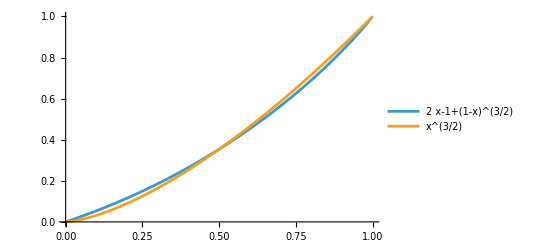

```mathematica
Plot[{2x-1+(1-x)^(3/2),x^(3/2)},{x,0,1},PlotLegends->"Expressions"]
```

```mathematica
Solve[2x-1+(1-x)^(3/2)==x^(3/2),x]
```

{{x→0},{x→1/2},{x→1}}

## 2025 - 08 - 23

```mathematica
f1[x_]:=2x-1+(1-x)^(3/2);
f2[x_]:=x^(3/2);
f3[a_,x_]:=a^3+(x-a^2)(x+a^2)^(1/2);
```

```mathematica
Manipulate[Plot[{f1[x]-f3[a,x]},{x,17/25,7/10},PlotLegends->"Expressions"],{a,17/100,23/100}]
```

```mathematica
Manipulate[Plot[{f1[x]-f3[a,x]},{x,17/25,7/10},PlotLegends->"Expressions"],{a,1/3,2/5}]
```

```mathematica
Block[{x=Sqrt[γ-2α*β]},Simplify[(β(α+x)^2)/2+((x-β)x^2)/2+(α*β^2)/2]]
```

1/2 (α^2 β+α β^2+γ √(-2 α β+γ))

```mathematica
Solve[γ/2==x^2/2+α*x,x]
```

{{x→-α-√(α^2+γ)},{x→-α+√(α^2+γ)}}

```mathematica
Block[{x=-α+√(α^2+γ)},Simplify[(x(x+α)^2)/2+(α*x^2)/2]]
```

1/2 (-α+√(α^2+γ)) (γ+α √(α^2+γ))

```mathematica
Expand[1/2 (-α+√(α^2+γ)) (γ+α √(α^2+γ))]
```

α^3/2-1/2 α^2 √(α^2+γ)+1/2 γ √(α^2+γ)

## 2025 - 08 - 31

```mathematica
Simplify[(q-p-1)^2-q^2+(p+1)((p+1)^2-(p+2)^2)+(p+1)^2]
```

-((1+p) (1+2 q))

```mathematica
Simplify[q((r+1)^2-r^2)+q((p+1)^2-(p+2)^2)]
```

-2 q (1+p-r)